Universal Quantum Computation: Demonstration |

Here we provide a simple demonstration that any arbitrary unitary operation can be implemented by combining CNOT gate and single-qubit rotations.

TwoLevelDecompositionpaclet:Q3/ref/TwoLevelDecompositionQ3 Package Symbol | Decomposes a unitary operator into a list of two-level unitary operators
TwoLevelUpaclet:Q3/ref/TwoLevelUQ3 Package Symbol | Represents a two-level unitary operator
GrayTwoLevelUpaclet:Q3/ref/GrayTwoLevelUQ3 Package Symbol | Rewrites a two-level unitary operators in terms of CNOT and controlled-unitary gates

Some functions conveniently used for the demonstration of universal quantum computation.

### Step 1. Decomposition into two-Level unitary operations

We first decompose the unitary operation into two-level unitary operations, that is, unitary operators acting only on a two-dimensional subspace.

```mathematica
<<Q3`
```

```mathematica
Let[Qubit,S]
```

Consider a 2^n×2^n unitary matrix.

```mathematica
n=2;
mat=RandomUnitary[2^n];
mat//MatrixForm
```

(0.0429006+0.489664 ⅈ | 0.229795+0.273092 ⅈ | 0.265758+0.215172 ⅈ | -0.0964376-0.710476 ⅈ
0.314083+0.0435907 ⅈ | 0.0684689+0.272054 ⅈ | -0.755416+0.438772 ⅈ | -0.232921+0.0576589 ⅈ
0.35213-0.30708 ⅈ | -0.719261-0.219828 ⅈ | 0.0724559+0.181801 ⅈ | -0.0470641-0.418962 ⅈ
-0.277856+0.601949 ⅈ | -0.439185-0.188068 ⅈ | 0.10315+0.26638 ⅈ | -0.356536+0.351404 ⅈ)

This is an explicit operator expression of the unitary transformation.

```mathematica
nn=Range[n];
SS=S[nn,None];
opU=ExpressionFor[mat,SS]
```

(-0.0431776+0.323731 ⅈ)-(0.11364-0.0968034 ⅈ) S_1^z S_2^z+(0.138429+0.346027 ⅈ) S_1^z S_2^++(0.105466-0.111395 ⅈ) S_1^z S_2^-+(0.249339+0.0787568 ⅈ) S_1^+S_2^z-(0.0964376+0.710476 ⅈ) S_1^+S_2^+-(0.755416-0.438772 ⅈ) S_1^+S_2^-+(0.395657-0.059506 ⅈ) S_1^-S_2^z-(0.719261+0.219828 ⅈ) S_1^-S_2^+-(0.277856-0.601949 ⅈ) S_1^-S_2^-+(0.0988623+0.0571284 ⅈ) S_1^z+(0.0164186+0.136416 ⅈ) S_1^+-(0.0435272+0.247574 ⅈ) S_1^-+(0.100856+0.0120017 ⅈ) S_2^z+(0.0913653-0.0729346 ⅈ) S_2^++(0.208616+0.154985 ⅈ) S_2^-

Here is a two-level decomposition, where the results are in terms of TwoLevelUpaclet:Q3/ref/TwoLevelUQ3 Package Symbol.

```mathematica
mm=TwoLevelDecomposition[mat]
```

{TwoLevelU[{{1.+0. ⅈ,0.+0. ⅈ},{0.+0. ⅈ,0.984506+0.175352 ⅈ}},{3,4},4],TwoLevelU[{{0.434153-0.378609 ⅈ,0.20713+0.790736 ⅈ},{-0.20713+0.790736 ⅈ,0.434153+0.378609 ⅈ}},{3,4},4],TwoLevelU[{{-0.36066-0.0500551 ⅈ,0.931353},{-0.931353,-0.36066+0.0500551 ⅈ}},{2,3},4],TwoLevelU[{{-0.157411-0.280809 ⅈ,-0.620273-0.715283 ⅈ},{0.620273-0.715283 ⅈ,-0.157411+0.280809 ⅈ}},{3,4},4],TwoLevelU[{{0.0429006+0.489664 ⅈ,0.870855},{-0.870855,0.0429006-0.489664 ⅈ}},{1,2},4],TwoLevelU[{{0.263873+0.313591 ⅈ,0.912158},{-0.912158,0.263873-0.313591 ⅈ}},{2,3},4],TwoLevelU[{{0.334557+0.270876 ⅈ,-0.121403-0.894404 ⅈ},{0.121403-0.894404 ⅈ,0.334557-0.270876 ⅈ}},{3,4},4]}

You can convert the above results to more human readable full matrix form by means of Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol.

```mathematica
MatrixForm/@Matrix/@mm
```

{(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1.+0. ⅈ | 0
0 | 0 | 0 | 0.984506+0.175352 ⅈ),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0.434153-0.378609 ⅈ | 0.20713+0.790736 ⅈ
0 | 0 | -0.20713+0.790736 ⅈ | 0.434153+0.378609 ⅈ),(1 | 0 | 0 | 0
0 | -0.36066-0.0500551 ⅈ | 0.931353 | 0
0 | -0.931353 | -0.36066+0.0500551 ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | -0.157411-0.280809 ⅈ | -0.620273-0.715283 ⅈ
0 | 0 | 0.620273-0.715283 ⅈ | -0.157411+0.280809 ⅈ),(0.0429006+0.489664 ⅈ | 0.870855 | 0 | 0
-0.870855 | 0.0429006-0.489664 ⅈ | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 0.263873+0.313591 ⅈ | 0.912158 | 0
0 | -0.912158 | 0.263873-0.313591 ⅈ | 0
0 | 0 | 0 | 1),(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 0.334557+0.270876 ⅈ | -0.121403-0.894404 ⅈ
0 | 0 | 0.121403-0.894404 ⅈ | 0.334557-0.270876 ⅈ)}

Check the decomposition with the original matrix.

```mathematica
new=Dot@@Matrix/@mm;
mat-new//Chop//MatrixForm
```

(0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)

### Step 2. Rewriting two-level unitary operators to elementary gates.

Now we rewrite each two-level unitary operator in terms of elementary gates, that is, in a combination of CNOT gates and one controlled-U gate.

GrayTwoLevelUpaclet:Q3/ref/GrayTwoLevelUQ3 Package Symbol does the job.

```mathematica
gates=Catenate[GrayTwoLevelU[#,S@nn]&/@mm]
```

{ControlledU[{S_1},(0.992253+0.0876761 ⅈ)+(0.00774712-0.0876761 ⅈ) S_2^z,Label→U],ControlledU[{S_1},(0.434153+0. ⅈ)-(0.+0.378609 ⅈ) S_2^z+(0.20713+0.790736 ⅈ) S_2^+-(0.20713-0.790736 ⅈ) S_2^-,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(-0.36066+0. ⅈ)-(0.+0.931353 ⅈ) S_2^y+(0.+0.0500551 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(-0.157411+0. ⅈ)-(0.+0.280809 ⅈ) S_2^z-(0.620273+0.715283 ⅈ) S_2^++(0.620273-0.715283 ⅈ) S_2^-,Label→U],{S_1^x},ControlledU[{S_1},(0.0429006+0. ⅈ)+(0.+0.489664 ⅈ) S_2^z+0.870855 S_2^+-0.870855 S_2^-,Label→U],{S_1^x},CNOT[{S_2},{S_1}],ControlledU[{S_1},(0.263873+0. ⅈ)-(0.+0.912158 ⅈ) S_2^y-(0.+0.313591 ⅈ) S_2^z,Label→U],CNOT[{S_2},{S_1}],ControlledU[{S_1},(0.334557+0. ⅈ)+(0.+0.270876 ⅈ) S_2^z-(0.121403+0.894404 ⅈ) S_2^++(0.121403-0.894404 ⅈ) S_2^-,Label→U]}

Here is a quantum circuit model of the decomposition. Here controlled-U gates are all labeled by the same character "U" but in fact they are different operators. Also do not forget to reverse the order of the elementary gates in the quantum circuit model.

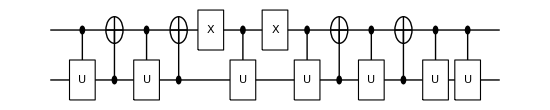

```mathematica
qc=QuantumCircuit[Reverse@gates]
```

```mathematica
new=ExpressionFor[qc]
```

(-0.0431776+0.323731 ⅈ)-(0.462243-0.0276041 ⅈ) S_1^x S_2^x+(0.492756+0.0543933 ⅈ) S_1^x S_2^y+(0.322498+0.00962535 ⅈ) S_1^x S_2^z+(0.163456+0.0363159 ⅈ) S_1^y S_2^x-(0.275096-0.0818678 ⅈ) S_1^y S_2^y-(0.0691314+0.0731591 ⅈ) S_1^y S_2^z+(0.121948+0.117316 ⅈ) S_1^z S_2^x-(0.228711-0.0164815 ⅈ) S_1^z S_2^y-(0.11364-0.0968034 ⅈ) S_1^z S_2^z-(0.0135543+0.0555792 ⅈ) S_1^x-(0.191995-0.0299729 ⅈ) S_1^y+(0.0988623+0.0571284 ⅈ) S_1^z+(0.149991+0.0410254 ⅈ) S_2^x+(0.11396-0.0586254 ⅈ) S_2^y+(0.100856+0.0120017 ⅈ) S_2^z

```mathematica
new-opU//Elaborate//Chop
```

0

| Related Guides
▪Quantum Computation and Information

| Related Tech Notes
▪Quantum Computation and Information: Overview
▪Universal Quantum Computation
▪QuantumCircuit Usage Examples
▪Quantum Fourier Transform
▪Quantum Teleportation

| Related Wolfram Education Group Courses
An Elementary Introduction to the Wolfram Languagehttps://www.wolfram.com/language/elementary-introduction/
The Wolfram Language: Fast Introduction for Programmershttps://www.wolfram.com/language/fast-introduction-for-programmers/